```mathematica
x[X_,Y_,Z_]:=X/(X+Y+Z)
y[X_,Y_,Z_]:=Y/(X+Y+Z)
z[X_,Y_,Z_]:=Z/(X+Y+Z)
sRGBMatrix=({{3.2404542, -1.5371385, -0.4985314}, {-0.9692660, 1.8760108, 0.0415560}, {0.0556434, -0.2040259, 1.0572252}})
```

{{3.24045,-1.53714,-0.498531},{-0.969266,1.87601,0.041556},{0.0556434,-0.204026,1.05723}}

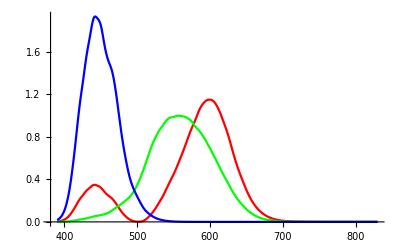

```mathematica
CMCs=Import["D:\\Apps\\Programming\\Projects\\Site\\project\\Mathematica\\media\\0001\\CMCs.csv"];
Xl=Table[List[CMCs⟦i,1⟧,CMCs⟦i,2⟧],{i,1,CMCs//Length}];
Yl=Table[List[CMCs⟦i,1⟧,CMCs⟦i,3⟧],{i,1,CMCs//Length}];
Zl=Table[List[CMCs⟦i,1⟧,CMCs⟦i,4⟧],{i,1,CMCs//Length}];
ListPlot[{Xl,Yl,Zl},PlotStyle->{Red,Green,Blue},Joined->True]
X=Interpolation[Xl];
Y=Interpolation[Yl];
Z=Interpolation[Zl];
x[t_]:=X[t]/(X[t]+Y[t]+Z[t])
y[t_]:=Y[t]/(X[t]+Y[t]+Z[t])
z[t_]:=Z[t]/(X[t]+Y[t]+Z[t])
```

```mathematica
xyzl=Table[List[x[t],y[t],z[t]],{t,390,830}];
Graphics3D[Line[xyzl]]
f[t_]:=sRGBMatrix.{x[t],y[t],z[t]}
```

-Graphics3D-

```mathematica
ParametricPlot3D[{f[t]⟦1⟧,f[t]⟦2⟧,f[t]⟦3⟧},{t,390,830}]
Table[RGBColor[ungamma⟦i⟧⟦1⟧,ungamma⟦i⟧⟦2⟧,ungamma⟦i⟧⟦3⟧],{i,1,440}]
```

-Graphics3D-

{RGBColor[0.10455454219934174, -0.09305409853188015, 0.8675011664749809],RGBColor[0.10428198815158485, -0.09273953054826606, 0.8673354950434664],RGBColor[0.10393051214456939, -0.09245293524732207, 0.86723982306813],RGBColor[0.10351061065479006, -0.09220043621197131, 0.8672145946612178],RGBColor[0.10302809205635538, -0.09198478636999974, 0.8672594257455231],RGBColor[0.10249359522849649, -0.09181101669070252, 0.8673736015152866],RGBColor[0.10191687338590522, -0.0916832768448054, 0.8675560084176862],RGBColor[0.10130885055544192, -0.09160523967939743, 0.8678044331718335],RGBColor[0.10067972077633786, -0.09158057403586034, 0.8681170496190114],RGBColor[0.1000415233061564, -0.09161290969738595, 0.8684910043226546],RGBColor[0.09940491642377686, -0.09170524453493671, 0.8689235575705636],RGBColor[0.09878082567513069, -0.09185581251867564, 0.8694071061097617],RGBColor[0.09817921556638143, -0.09204607851325267, 0.8699179457515965],RGBColor[0.09760569515191198, -0.09225281316610043, 0.8704300544372897],RGBColor[0.09706569191574693, -0.09245385955441766, 0.8709185700107871],RGBColor[0.09656130767962995, -0.09262733013163205, 0.8713606789551364],RGBColor[0.09608560662215904, -0.09275621815701766, 0.8717432458641909],RGBColor[0.09559795240248559, -0.0928397065522755, 0.8720872320700513],RGBColor[0.09505136974407152, -0.09288123104098187, 0.8724212089185043],RGBColor[0.09440072489500578, -0.09288384805859425, 0.8727723853366258],RGBColor[0.09360284594835538, -0.09285072307239692, 0.8731670272271318],RGBColor[0.09263204336260134, -0.09278470131160554, 0.8736217169955182],RGBColor[0.0915257580531384, -0.09268733259370765, 0.8741179313015319],RGBColor[0.09033385893768764, -0.09255949859066903, 0.874629826458301],RGBColor[0.08910336944733754, -0.09240175170663968, 0.8751327569920658],RGBColor[0.08787946452346862, -0.09221470653564025, 0.8756031293797806],RGBColor[0.08668983035293426, -0.09199629084373788, 0.8760240574412126],RGBColor[0.08550968566453526, -0.09173730930557145, 0.8763997064879046],RGBColor[0.08430065497449835, -0.09142625591211681, 0.8767392353771152],RGBColor[0.08302281332546724, -0.09105087061934311, 0.8770518859552897],RGBColor[0.08163521164296028, -0.09059817504617171, 0.8773467369696906],RGBColor[0.08010700967032591, -0.0900590457156073, 0.8776312710281106],RGBColor[0.0784604610207052, -0.08944455839339194, 0.877904540263771],RGBColor[0.07673239546240146, -0.08877145775701706, 0.8781634047172603],RGBColor[0.07496379243247409, -0.08805786796161473, 0.8784038681092777],RGBColor[0.07320043856507902, -0.08732366962629992, 0.8786210991096541],RGBColor[0.07147535543140215, -0.08658243077311878, 0.8788108503860823],RGBColor[0.06976114601493522, -0.08581772135513054, 0.8789715200505911],RGBColor[0.0680088456971818, -0.08500319605825701, 0.8791032364412272],RGBColor[0.06616420718586835, -0.08411008828554847, 0.8792065589422458],RGBColor[0.06416598708442817, -0.08310656536609184, 0.8792827570585865],RGBColor[0.06196564956029871, -0.08196910896978749, 0.879334530547532],RGBColor[0.059596927459796334, -0.08072154216521538, 0.8793674123123051],RGBColor[0.05712292323417839, -0.07940377598678561, 0.8793871413747724],RGBColor[0.05462073019212249, -0.0780618045713723, 0.8793979886421956],RGBColor[0.052181508256533726, -0.0767481264517248, 0.8794031337627034],RGBColor[0.04988211850842983, -0.07550490613853242, 0.8794031774414202],RGBColor[0.04769521782691394, -0.07431047257234658, 0.8793912958131965],RGBColor[0.045555779956086506, -0.07312202984396124, 0.8793599220323812],RGBColor[0.043388377911910025, -0.0718917534071025, 0.8793020787804147],RGBColor[0.041107506976409636, -0.0705666684546562, 0.8792110847095488],RGBColor[0.0386368457112119, -0.06910101812849814, 0.8790824904922979],RGBColor[0.035980069181943575, -0.06749874502890371, 0.8789182337698837],RGBColor[0.03316552569634307, -0.0657786312011147, 0.8787217372733562],RGBColor[0.030227565316860217, -0.06396236983131379, 0.8784960928196713],RGBColor[0.027207251961556544, -0.06207511744610929, 0.8782442269548902],RGBColor[0.0241389916176048, -0.0601347569679964, 0.8779654261015364],RGBColor[0.02099950551776425, -0.05811485347747359, 0.8776459686028919],RGBColor[0.01774528432471445, -0.0559734896374621, 0.8772676304535357],RGBColor[0.014325651313042698, -0.05366318032011453, 0.8768105106863834],RGBColor[0.010682008130660614, -0.051129979282663815, 0.8762525502984486],RGBColor[0.0067540772121338355, -0.04832261540403685, 0.8755752405936552],RGBColor[0.002508808743106161, -0.045226946652378676, 0.87478227527302],RGBColor[-0.002081639066544072, -0.04183902157872317, 0.8738846552630073],RGBColor[-0.0070465700088270244, -0.038155837284612346, 0.8728951046378457],RGBColor[-0.012417366527721574, -0.034175876378875786, 0.8718289330384046],RGBColor[-0.018220798617098966, -0.029897385258922167, 0.8706987449308287],RGBColor[-0.02445207214171985, -0.025312456976056927, 0.8694941371861113],RGBColor[-0.031091384268028155, -0.020412634757166356, 0.8681961209588669],RGBColor[-0.038111659601981096, -0.015190728347999644, 0.8667830660667354],RGBColor[-0.04547419400900482, -0.009641826516894957, 0.8652293704126826],RGBColor[-0.05315154433396252, -0.0037535301784416275, 0.8635080455707382],RGBColor[-0.06120466506709166, 0.00252810865478182, 0.8615982931114751],RGBColor[-0.06973138394095701, 0.009276751271715844, 0.8594795363693135],RGBColor[-0.07884668849741211, 0.016578109202422094, 0.857128451969975],RGBColor[-0.08868617906046034, 0.024531982907855382, 0.8545187997091319],RGBColor[-0.09938907004334363, 0.03324409419828051, 0.8516204084125066],RGBColor[-0.11103252563035426, 0.04279141089950372, 0.8483983545969003],RGBColor[-0.12367603347411843, 0.05324642872305105, 0.8448126758009992],RGBColor[-0.13737970841880642, 0.06468703070984266, 0.8408184074997636],RGBColor[-0.1522017194144785, 0.07719652857248822, 0.8363641636080525],RGBColor[-0.16820587989266442, 0.0908651767731738, 0.8313947027912026],RGBColor[-0.1854846956793921, 0.10579722496696915, 0.8258562884222271],RGBColor[-0.20414519040885706, 0.12210711089283799, 0.8196928668465308],RGBColor[-0.22430209469417764, 0.1399177185290807, 0.8128441443982691],RGBColor[-0.24607827325556458, 0.15936039502033542, 0.8052457994622263],RGBColor[-0.26957931231766324, 0.18055523283635683, 0.7968354052519621],RGBColor[-0.29480733079857924, 0.20354113925664563, 0.7875755453645567],RGBColor[-0.3217110454156433, 0.22831231726712778, 0.7774444887756086],RGBColor[-0.35020383723601245, 0.25483028731996965, 0.7664339571386243],RGBColor[-0.3801608057236069, 0.28301841380605514, 0.7545529699811879],RGBColor[-0.41145795799086343, 0.31280003240596427, 0.7418110615519118],RGBColor[-0.4441098849248577, 0.3442412483819094, 0.72815054795546],RGBColor[-0.4781659314662053, 0.3774527689867133, 0.713488170530966],RGBColor[-0.5136671891308424, 0.41254948025145755, 0.6977321082623237],RGBColor[-0.5506410005760586, 0.4496467932959869, 0.6807826538863597],RGBColor[-0.5890553875507594, 0.48881532330732747, 0.6625527053692104],RGBColor[-0.628689252161932, 0.5299412161726712, 0.6430366227296762],RGBColor[-0.6692309978429106, 0.5728200347568438, 0.622270036245271],RGBColor[-0.7103169494265589, 0.6171922592765059, 0.6003152541740073],RGBColor[-0.7515368711341213, 0.6627446001107153, 0.5772629182101536],RGBColor[-0.7924629572598642, 0.7091376712741488, 0.5532201147586323],RGBColor[-0.8327225547841921, 0.7560858305555036, 0.5282702258219238],RGBColor[-0.8719424765336823, 0.8032982302007033, 0.5025015051863935],RGBColor[-0.9097342170632532, 0.8504601921602045, 0.4760176123206109],RGBColor[-0.945700263183674, 0.8972367616534305, 0.4489374721637578],RGBColor[-0.979544027944675, 0.9433586865561316, 0.4213689788958492],RGBColor[-1.0113918985443644, 0.9888730758927516, 0.3933331661410846],RGBColor[-1.0415052015633348, 1.0339222334408922, 0.36482903682497325],RGBColor[-1.0701702746320767, 1.078656145580005, 0.3358613811838029],RGBColor[-1.0976892091728483, 1.1232229344823228, 0.30644527672201805],RGBColor[-1.1242419312985996, 1.167667811684771, 0.2766323207078106],RGBColor[-1.149480511596232, 1.2116433623827332, 0.24658034873736276],RGBColor[-1.1729011531207592, 1.2546756923233058, 0.21648901354915018],RGBColor[-1.1939812739870643, 1.2962644845425995, 0.18657408501171469],RGBColor[-1.2121912328896145, 1.335893474209331, 0.15706335298770752],RGBColor[-1.2269230831159603, 1.3729395114270664, 0.1282485631677245],RGBColor[-1.2373126820930809, 1.406427484744264, 0.10063294832510034],RGBColor[-1.242634620716047, 1.4354851018608388, 0.07469218851685916],RGBColor[-1.2424106851151027, 1.4594825843150099, 0.05079410184430616],RGBColor[-1.2363959281500945, 1.47803011748575, 0.029193708935896845],RGBColor[-1.2247715121510956, 1.4911516052213374, 0.009964382271400007],RGBColor[-1.2086859555077658, 1.4997488127382697, -0.007172080676261988],RGBColor[-1.189412905265041, 1.5048394347867906, -0.02254171447186154],RGBColor[-1.168100944299678, 1.5073329469417338, -0.03643032696872811],RGBColor[-1.1457779229217195, 1.508033574161648, -0.049084120073445314],RGBColor[-1.1231424973025472, 1.507491245794899, -0.0606736906224183],RGBColor[-1.099965005977546, 1.505586949963973, -0.07120415591911207],RGBColor[-1.075820586437029, 1.5020766178966822, -0.0806612986248383],RGBColor[-1.0503143715457177, 1.4967520715756606, -0.08905039402798334],RGBColor[-1.023078751824916, 1.4894355307406886, -0.09639223399353077],RGBColor[-0.9939004009361032, 1.4800606361902486, -0.1027353556318902],RGBColor[-0.9630831801741354, 1.4689060493458719, -0.10819307917269622],RGBColor[-0.931024415632083, 1.4563030024368695, -0.11288074126987899],RGBColor[-0.8980825562515462, 1.442547040305015, -0.11689914587530584],RGBColor[-0.8645808771653856, 1.4279017455255973, -0.12033627123936219],RGBColor[-0.8308004704212604, 1.412591411872147, -0.12326376557369197],RGBColor[-0.7969525607934348, 1.3967758674320492, -0.1257268321360716],RGBColor[-0.7632254299594179, 1.380598133297045, -0.127766312603547],RGBColor[-0.729793978046112, 1.3641944158239594, -0.12942346538697802],RGBColor[-0.6968190293561936, 1.3476928060417228, -0.13073904888469168],RGBColor[-0.6643806386709912, 1.3311763568457449, -0.13175246738483898],RGBColor[-0.6322787551953301, 1.3145716816917572, -0.1324981825150806],RGBColor[-0.6002523942930076, 1.2977644104391695, -0.13300269228988135],RGBColor[-0.5680495315752296, 1.280638048988138, -0.13328558972300028],RGBColor[-0.5354307129979838, 1.2630774594367458, -0.13336107705974445],RGBColor[-0.5022445468316302, 1.2450122499502965, -0.13324051414144464],RGBColor[-0.46864177408296914, 1.2265394424811367, -0.13293927643428713],RGBColor[-0.43483653481282386, 1.2077931985825305, -0.13247557342239002],RGBColor[-0.4010302671959908, 1.1889019863362182, -0.13186877820655205],RGBColor[-0.36741029732865205, 1.16998707901719, -0.13113869540468956],RGBColor[-0.33411630312250923, 1.1511428494564744, -0.1303040026372949],RGBColor[-0.30114759817962067, 1.132382842989318, -0.12937848915501915],RGBColor[-0.26847045742315845, 1.1136999997197528, -0.1283732278267081],RGBColor[-0.23605142540048815, 1.095085805399047, -0.1272977060118851],RGBColor[-0.20385944722401012, 1.0765317219070332, -0.12616010131286412],RGBColor[-0.171867811633478, 1.0580308175678015, -0.12496785599048324],RGBColor[-0.14006142079759654, 1.0395829007910309, -0.12372886887695406],RGBColor[-0.10842893137609526, 1.0211887947544114, -0.12245003282558828],RGBColor[-0.07695944746237438, 1.0028483545590272, -0.12113704174979065],RGBColor[-0.04564290201914912, 0.9845608697837864, -0.11979458514325235],RGBColor[-0.01443010803053576, 0.9663011109356727, -0.1184240161144894],RGBColor[0.01687810269004418, 0.9479526416305073, -0.11701666712690532],RGBColor[0.0485006333294458, 0.929387049253602, -0.1155625769291988],RGBColor[0.08063450765774166, 0.9104891015178763, -0.11405312220251516],RGBColor[0.1134554759190555, 0.891156275743317, -0.11248087574926445],RGBColor[0.14702556216891513, 0.8713539665986343, -0.11084477799832275],RGBColor[0.18103551118436936, 0.8512691181029829, -0.10916438039802945],RGBColor[0.2151144114421181, 0.8311251901673279, -0.10746238408829645],RGBColor[0.24892515501977017, 0.8111251341201693, -0.10575927939985928],RGBColor[0.28216422832454, 0.7914515964802161, -0.10407343564698072],RGBColor[0.3146704609135463, 0.7722021566796945, -0.10241519310368702],RGBColor[0.3467334360809635, 0.7532055831242944, -0.10077002986740702],RGBColor[0.37871926027002084, 0.734244936122157, -0.09911913108952512],RGBColor[0.41095513429212516, 0.7151263167904315, -0.0974456683934033],RGBColor[0.44373125038639327, 0.6956778007050567, -0.09573475962269466],RGBColor[0.4772079085249639, 0.6758047256935901, -0.09397848874029982],RGBColor[0.5111630343550313, 0.6556400771696962, -0.09218964904109467],RGBColor[0.5453059266954301, 0.6353576598967986, -0.09038471316597467],RGBColor[0.5793743915361305, 0.6151142182796938, -0.08857852208400753],RGBColor[0.613134197258689, 0.5950498019273829, -0.08678435544759668],RGBColor[0.6464316534485485, 0.5752564426326537, -0.08501106403339546],RGBColor[0.6793387972756297, 0.555691668556852, -0.08325515820477347],RGBColor[0.7119686849284376, 0.536288539135845, -0.08151087923781843],RGBColor[0.7444184548497517, 0.5169895770474222, -0.07977331720300071],RGBColor[0.7767707213189678, 0.4977458849474517, -0.07803828238803084],RGBColor[0.8090861475115902, 0.478521648524673, -0.07630278820132867],RGBColor[0.8413817567823668, 0.4593070764161033, -0.07456625305754414],RGBColor[0.8736598646268294, 0.44010109382580925, -0.07282885251379112],RGBColor[0.9059176262945771, 0.4209056368191194, -0.07109098086060779],RGBColor[0.9381462584849856, 0.40172614997003775, -0.06935332724326293],RGBColor[0.9702744492650455, 0.38260524831664444, -0.06761991173483661],RGBColor[1.0020118697265152, 0.3637159001929994, -0.06590657763837104],RGBColor[1.0330555594338549, 0.34523857480518877, -0.06422983321337286],RGBColor[1.0631488819196449, 0.3273261689642373, -0.06260368446374821],RGBColor[1.0920743821200063, 0.31010827404078045, -0.061040036453978326],RGBColor[1.1197308994931299, 0.2936451980522645, -0.059544449090760024],RGBColor[1.1463368239367846, 0.27780700268279723, -0.058105174373657247],RGBColor[1.1721543433940496, 0.2624376452255287, -0.056708063366708625],RGBColor[1.1974120001690598, 0.24740109243099945, -0.055340768008939695],RGBColor[1.222305674206654, 0.23258077469702737, -0.053992727086283276],RGBColor[1.2469563839342508, 0.21790467334763683, -0.05265741595751404],RGBColor[1.2712884825620092, 0.20341788971522004, -0.051338995860086],RGBColor[1.2951915693296467, 0.18918621418501888, -0.0500435085002892],RGBColor[1.318570648801735, 0.17526626226071906, -0.04877615798464213],RGBColor[1.3413475679166873, 0.16170460602146056, -0.04754122011631507],RGBColor[1.3634790877084793, 0.14852703763653968, -0.04634108599032382],RGBColor[1.385025412309033, 0.1356977202141739, -0.04517250070813961],RGBColor[1.4060567175105922, 0.12317489674470161, -0.04403168569354292],RGBColor[1.4266360394456907, 0.1109210482375932, -0.04291523657174483],RGBColor[1.446817607578159, 0.09890389298637298, -0.04182022019872444],RGBColor[1.4666165521136239, 0.08711445293568228, -0.040745846606377464],RGBColor[1.4859395499126633, 0.075608302717875, -0.03969718447833386],RGBColor[1.5046809701273554, 0.0644483734028776, -0.038679997826653455],RGBColor[1.522756956830219, 0.05368461578381778, -0.037698854969053605],RGBColor[1.5400956746257597, 0.043359808767955775, -0.03675765790450429],RGBColor[1.556661424310573, 0.03349523900456236, -0.035858372826362624],RGBColor[1.572492678643079, 0.02406799512492991, -0.034998909607537716],RGBColor[1.5876407385685862, 0.015047532737865237, -0.03417648758252923],RGBColor[1.6021541457489743, 0.006404964764650335, -0.033388489960674055],RGBColor[1.616076758849818, -0.00188582864198373, -0.032632532968767364],RGBColor[1.6294441579528118, -0.009846022900020969, -0.03190669680841542],RGBColor[1.642284232474293, -0.01749223648934044, -0.031209456684709577],RGBColor[1.6546195944968187, -0.024837914879666433, -0.030539604472921696],RGBColor[1.6664704433213562, -0.03189509704194756, -0.02989603304078158],RGBColor[1.6778599282643982, -0.038677555351513945, -0.02927749816968038],RGBColor[1.6888250408236394, -0.045199273087928704, -0.028689962620659162],RGBColor[1.6993921515663537, -0.0514924749004807, -0.02811562436667133],RGBColor[1.7096258404895424, -0.057587108641771745, -0.027559408086639293],RGBColor[1.7195720524730806, -0.06351053660678918, -0.027018816607709543],RGBColor[1.7292699813067132, -0.06928610050498119, -0.026491719688861867],RGBColor[1.7387277910844108, -0.07491866243084333, -0.025977673599393437],RGBColor[1.7478518401891192, -0.08035245448257844, -0.025481767901072747],RGBColor[1.756538721632218, -0.08552589302923352, -0.025009622918200455],RGBColor[1.764703267749295, -0.09038825679863782, -0.024565867640560478],RGBColor[1.772273568341293, -0.0948967199506846, -0.024154410494890935],RGBColor[1.7792207331607452, -0.0990340770105621, -0.023776821709297756],RGBColor[1.7856373796129534, -0.10285548591473048, -0.02342806738945121],RGBColor[1.79163313023589, -0.1064262319404492, -0.02310218938665859],RGBColor[1.7973062977372967, -0.10980486483945417, -0.02279384425839493],RGBColor[1.802743739000788, -0.11304311189186067, -0.022498311203289198],RGBColor[1.8080114759314916, -0.11618029218716597, -0.02221200183217434],RGBColor[1.8131220170679812, -0.11922385513699607, -0.02193423628729367],RGBColor[1.8180756682132584, -0.12217398286114312, -0.021664997947797186],RGBColor[1.8228733971842899, -0.12503125173924645, -0.021404234211387124],RGBColor[1.827515810984089, -0.12779602326959627, -0.021151912086542955],RGBColor[1.8320147330934444, -0.13047533888031304, -0.02090738894942184],RGBColor[1.8364173131017174, -0.13309727832644513, -0.02066810214941015],RGBColor[1.840775971903356, -0.13569306066833853, -0.0204312025325884],RGBColor[1.8451364926055125, -0.13828995185786297, -0.02019420171869219],RGBColor[1.8495385573642247, -0.14091158444911756, -0.019954942923263816],RGBColor[1.853982695910979, -0.14355827392163512, -0.019713397354605623],RGBColor[1.8583363285464618, -0.14615106294977076, -0.019476770917422552],RGBColor[1.862452402387534, -0.14860237475939608, -0.019253056155580345],RGBColor[1.8662040572073268, -0.15083665823449555, -0.019049148111912807],RGBColor[1.8694772847471515, -0.15278601619884935, -0.018871243305584935],RGBColor[1.8722138332214937, -0.15441575702755583, -0.01872250780815577],RGBColor[1.8745203140737945, -0.1557893727522065, -0.01859714712841839],RGBColor[1.8765338819884052, -0.15698854531303763, -0.018487706704397],RGBColor[1.878380159577091, -0.15808808876919045, -0.01838735875948746],RGBColor[1.8801751011099883, -0.15915705923645285, -0.018289801005895723],RGBColor[1.8820083648358985, -0.16024885233711061, -0.018190160383868142],RGBColor[1.8838799350859166, -0.16136345873960867, -0.01808843774503309],RGBColor[1.8857742779998699, -0.16249162731377675, -0.017985477377895437],RGBColor[1.8876751375916128, -0.16362367687012414, -0.017882162819585316],RGBColor[1.8895662575948167, -0.16474992605229732, -0.017779377622461262],RGBColor[1.8914339206948312, -0.16586220556676656, -0.017677867343065402],RGBColor[1.8932691935731933, -0.16695519521037372, -0.017578117520600782],RGBColor[1.8950645625111446, -0.16802442021705832, -0.017480536536905865],RGBColor[1.8968121132934321, -0.1690651673066258, -0.01738555454140194],RGBColor[1.8985052470393597, -0.1700735065412754, -0.01729353019311218],RGBColor[1.9001358150645027, -0.17104458500360653, -0.01720490638520758],RGBColor[1.9016867217354203, -0.17196822145543866, -0.01712061229090303],RGBColor[1.9031413466485962, -0.17283451767992863, -0.017041551253957198],RGBColor[1.9044810268782406, -0.17363235904401686, -0.01696873763226532],RGBColor[1.905691903440253, -0.17435349188348181, -0.01690292468231582],RGBColor[1.9067650573436832, -0.17499260452786003, -0.016844597164590018],RGBColor[1.9077189426691015, -0.17556068723325158, -0.016792752072242192],RGBColor[1.908576366608215, -0.17607132273420634, -0.016746149800333857],RGBColor[1.909359606843978, -0.17653777841839313, -0.016703579523517968],RGBColor[1.9100901719525063, -0.17697286363488385, -0.016663872218553304],RGBColor[1.9107845003905906, -0.17738636824285559, -0.016626134430757472],RGBColor[1.911444226282541, -0.17777926543870193, -0.01659027734303322],RGBColor[1.9120678035967402, -0.17815063448929014, -0.01655638498450842],RGBColor[1.9126527471854413, -0.1784989953745202, -0.016524592426675366],RGBColor[1.9131979164376536, -0.17882366880794087, -0.016494961663445253],RGBColor[1.9137019636588772, -0.1791238521753198, -0.016467565944027394],RGBColor[1.9141679133576972, -0.17940134671101315, -0.016442240881862143],RGBColor[1.9145994973563691, -0.17965837488728975, -0.016418783646835314],RGBColor[1.9150005415613647, -0.17989721520790714, -0.016396986295215084],RGBColor[1.9153738072980542, -0.1801195121694794, -0.016376698744842606],RGBColor[1.9157229028801583, -0.18032741468924463, -0.016357724878477246],RGBColor[1.9160464591005648, -0.18052010734121948, -0.01634013911457074],RGBColor[1.9163439552118762, -0.1806972799963108, -0.016323969756522103],RGBColor[1.9166141655776177, -0.18085820273147057, -0.016309283419504543],RGBColor[1.916856379383562, -0.1810024522240431, -0.016296118737333144],RGBColor[1.9170699931540274, -0.1811296690764268, -0.01628450850981268],RGBColor[1.917260740445752, -0.1812432678860968, -0.016274141109569637],RGBColor[1.9174330187826196, -0.1813458675813432, -0.01626477752461198],RGBColor[1.9175917202191881, -0.18144038160628195, -0.01625615186446671],RGBColor[1.9177455188945007, -0.18153197581077307, -0.016247792676719407],RGBColor[1.9178937073236562, -0.18162022885492712, -0.01623973841423136],RGBColor[1.9180359284645698, -0.1817049281037163, -0.016232008482773168],RGBColor[1.9181631266952737, -0.1817806805166049, -0.016225095068926006],RGBColor[1.918271974421795, -0.1818455043579097, -0.01621917903239313],RGBColor[1.918353461727723, -0.1818940338068622, -0.016214750075590444],RGBColor[1.9184067610047708, -0.18192577598455795, -0.016211853180264572],RGBColor[1.918435779949343, -0.18194305810443234, -0.01621027595727865],RGBColor[1.9184462151014836, -0.18194927271881112, -0.016209708791171812],RGBColor[1.9184492853322253, -0.18195110118281965, -0.016209541919544712],RGBColor[1.9184506076336145, -0.18195188867428302, -0.016209470050488936],RGBColor[1.9184537765785679, -0.18195377592715756, -0.01620929781359695],RGBColor[1.9184619905525866, -0.1819586677275219, -0.016208851371839042],RGBColor[1.918464615785989, -0.1819602311750913, -0.016208708686482054],RGBColor[1.9184636399461827, -0.18195965001748005, -0.016208761724833237],RGBColor[1.9184561899290942, -0.1819552131887019, -0.01620916664439081],RGBColor[1.918430665357598, -0.1819400121291581, -0.016210553942980176],RGBColor[1.9183910362143315, -0.18191641114660895, -0.01621270784611461],RGBColor[1.9183360028848628, -0.18188363626072046, -0.01621569898977987],RGBColor[1.9182610493266126, -0.18183899795985248, -0.016219772827636196],RGBColor[1.9181590407441154, -0.18177824714424207, -0.016225317146475043],RGBColor[1.9180364599987727, -0.18170524465684912, -0.01623197959309522],RGBColor[1.9178960182257778, -0.18162160510372183, -0.016239612813249003],RGBColor[1.9177456355409497, -0.18153204527911315, -0.016247786336810663],RGBColor[1.9175897189920392, -0.1814391897832165, -0.016256260634151663],RGBColor[1.9174309115461048, -0.18134461262481083, -0.01626489205606435],RGBColor[1.9172814240304594, -0.18125558591473678, -0.016273016925843722],RGBColor[1.9171282653214052, -0.18116437283966869, -0.016281341330468865],RGBColor[1.916980995158331, -0.18107666666531697, -0.016289345683823737],RGBColor[1.9168290030746844, -0.18098614836948512, -0.01629760668061527],RGBColor[1.9166621595632856, -0.18088678536346436, -0.016306674874690216],RGBColor[1.9164917085726558, -0.18078527393718147, -0.016315939140650167],RGBColor[1.916317283585368, -0.18068139581260423, -0.01632541939926481],RGBColor[1.9161206172100176, -0.1805642719156414, -0.01633610851054481],RGBColor[1.9159249526995388, -0.1804477446754168, -0.01634674316897245],RGBColor[1.9157284741880478, -0.18033073266004696, -0.016357422069571033],RGBColor[1.915537084035224, -0.180216750996943, -0.016367824410275136],RGBColor[1.915334855740134, -0.18009631472025434, -0.016378815820201342],RGBColor[1.9151298531919942, -0.17997422624792336, -0.01638995801492498],RGBColor[1.9149051737081353, -0.17984041925285232, -0.016402169680498332],RGBColor[1.9147030707060373, -0.17972005759391907, -0.016413154280563266],RGBColor[1.9145090036317343, -0.1796044817006126, -0.01642370211594848],RGBColor[1.9142747314351423, -0.1794649618026838, -0.016436435159788446],RGBColor[1.9140653085853352, -0.17934024083684152, -0.016447817604510723],RGBColor[1.9138583132380662, -0.17921696556071887, -0.016459068110843918],RGBColor[1.9136093979011635, -0.1790687249973797, -0.01647259703123362],RGBColor[1.9133650604482098, -0.17892321077506845, -0.016485877136792282],RGBColor[1.913055565593939, -0.1787388923151515, -0.016502698644444445],RGBColor[1.9128031570966197, -0.17858857141367612, -0.01651641742332089],RGBColor[1.912499261814043, -0.1784075877569602, -0.016532934585886887],RGBColor[1.9121903419085475, -0.17822361170555567, -0.016549724844214297],RGBColor[1.911841522807702, -0.17801587384313144, -0.016568683683410253],RGBColor[1.9114873593018051, -0.17780495314100997, -0.01658793299900422],RGBColor[1.9111727257670232, -0.17761757435984715, -0.01660503380161836],RGBColor[1.910835904547716, -0.1774169817892326, -0.01662334053803033],RGBColor[1.9104520429346181, -0.1771883744945677, -0.016644203990113626],RGBColor[1.910100672941894, -0.17697911745838024, -0.016663301474093714],RGBColor[1.9098158600421402, -0.176809498240733, -0.016678781480648074],RGBColor[1.9094133299295541, -0.17656977299361387, -0.01670065959356551],RGBColor[1.9090898195140904, -0.17637710762059466, -0.01671824286790498],RGBColor[1.9088080488751424, -0.17620930020956949, -0.01673355752304001],RGBColor[1.908444800506226, -0.1759929690525176, -0.016753300614510018],RGBColor[1.9081009046044042, -0.17578816318217438, -0.01677199187048481],RGBColor[1.9077838662179811, -0.17559935220094514, -0.01678922338037802],RGBColor[1.90737968776346, -0.17535864529018064, -0.01681119108314188],RGBColor[1.9071368619517932, -0.17521403131997437, -0.016824389028738507],RGBColor[1.9067186901855244, -0.17496499074667893, -0.016847117288899066],RGBColor[1.9063280809381766, -0.17473236492461075, -0.016868347484983448],RGBColor[1.9059626153371818, -0.17451471330359491, -0.01688821108632905],RGBColor[1.9056175202443362, -0.1743091932596892, -0.016906967520127318],RGBColor[1.9052077480763447, -0.17406515503456566, -0.016929239249574186],RGBColor[1.9047776135227883, -0.17380899006970507, -0.01695261770509384],RGBColor[1.9044941681799914, -0.17364018529529923, -0.016968023382884688],RGBColor[1.9041015708126032, -0.17340637545605297, -0.016989361636263134],RGBColor[1.9039087492606952, -0.173291541328777, -0.01699984177564566],RGBColor[1.9034400646847989, -0.17301241804764922, -0.017025315482465386],RGBColor[1.903115878296146, -0.1728193501014198, -0.017042935496957394],RGBColor[1.9028816793336005, -0.17267987381774375, -0.017055664560417516],RGBColor[1.902416786592898, -0.17240300874935666, -0.017080932175330243],RGBColor[1.9022027525939507, -0.1722755416315307, -0.01709256524289643],RGBColor[1.9019045211206893, -0.17209793103448268, -0.017108774568965528],RGBColor[1.9014472807289486, -0.17182562329283624, -0.0171336262672811],RGBColor[1.9010372501680108, -0.17158143118279578, -0.017155912040770598],RGBColor[1.900851312145167, -0.1714706965145525, -0.01716601805006588],RGBColor[1.900330578735117, -0.17116057575214427, -0.017194320688772247],RGBColor[1.9001666021748052, -0.17106292014772262, -0.01720323305977295],RGBColor[1.899546903066589, -0.17069386074766357, -0.01723691463200934],RGBColor[1.8992449703069016, -0.17051404586384178, -0.01725332512852469],RGBColor[1.8987905803589231, -0.1702434356929211, -0.017278021900963787],RGBColor[1.898766668196315, -0.1702291948972361, -0.017279321562721467],RGBColor[1.898251225335349, -0.16992222490081232, -0.017307336652182134],RGBColor[1.897839007312651, -0.16967673005640604, -0.0173297413174859],RGBColor[1.8969807640601504, -0.16916560661654145, -0.017376388120300748],RGBColor[1.8971667932859764, -0.16927639560036667, -0.017366277153987163],RGBColor[1.8966103100439882, -0.168944984164223, -0.01739652284946236],RGBColor[1.8960560457529962, -0.16861489421573728, -0.017426647941636272],RGBColor[1.8960926985833333, -0.16863672266666674, -0.01742465580555555],RGBColor[1.8954303226465365, -0.16824224724689163, -0.017460656927175848],RGBColor[1.8945897580126185, -0.1677416522397478, -0.017506342870662446],RGBColor[1.8942461695359785, -0.16753702945527915, -0.017525017417619373],RGBColor[1.8945087296774195, -0.16769339612903233, -0.017510746881720433],RGBColor[1.8936767314744074, -0.1671979028265851, -0.017555967226890755],RGBColor[1.8929280538461537, -0.16675203076923073, -0.017596658974358977],RGBColor[1.8922908503250975, -0.16637254668400503, -0.017631291937581284],RGBColor[1.8921358906697459, -0.16628026106235572, -0.017639714226327943],RGBColor[1.8915421440236098, -0.16592665755041802, -0.01767198524348254],RGBColor[1.8915162925615505, -0.16591126181246718, -0.017673390309062342],RGBColor[1.8902649586956521, -0.16516603478260872, -0.01774140217391304],RGBColor[1.890819704332344, -0.16549641139465865, -0.017711250919881308],RGBColor[1.8892158606060603, -0.16454124848484852, -0.017798422222222228],RGBColor[1.8896371907991938, -0.1647921700470113, -0.017775522296843524],RGBColor[1.889077979142857, -0.16445913371428555, -0.01780591628571429],RGBColor[1.8883737166160852, -0.16403971289833086, -0.017844194006069805],RGBColor[1.886995735351089, -0.16321906150121057, -0.017919089346246975],RGBColor[1.8883053226415092, -0.16399898113207534, -0.017847911320754722],RGBColor[1.8860044919781218, -0.16262873035551484, -0.01797296490428442],RGBColor[1.887343561396702, -0.1634262079534432, -0.017900184481086323],RGBColor[1.8845842386996898, -0.1617829040247677, -0.018050157791537666],RGBColor[1.88741477453348, -0.16346861866081241, -0.017896313940724475],RGBColor[1.8857808906651108, -0.16249556546091015, -0.017985117969661617],RGBColor[1.883048829900744, -0.16086849727047137, -0.018133609553349875],RGBColor[1.8853322600263849, -0.1622283852242744, -0.01800950171503958],RGBColor[1.8802139221598875, -0.15918017896213177, -0.018287691023842922],RGBColor[1.8805135059612514, -0.15935859493293592, -0.018271408196721316],RGBColor[1.8797474183544303, -0.1589023544303797, -0.01831304620253165],RGBColor[1.8834572818487394, -0.16111174924369753, -0.018111409579831927],RGBColor[1.8778609165775402, -0.1577788556149733, -0.018415580392156863],RGBColor[1.8831835465909086, -0.16094872727272713, -0.01812628750000001],RGBColor[1.8781687313253008, -0.1579621734939759, -0.018398850200803216],RGBColor[1.8783320259574467, -0.15805942297872333, -0.01838997489361703],RGBColor[1.8815903620767498, -0.15999991241534983, -0.01821287945823928],RGBColor[1.880326134688995, -0.15924700669856462, -0.01828159210526315],RGBColor[1.8789010641221369, -0.15839831145038163, -0.018359046819338427],RGBColor[1.875427714285714, -0.1563297714285714, -0.018547828571428567],RGBColor[1.875427714285714, -0.15632977142857152, -0.018547828571428553],RGBColor[1.8795641581818179, -0.15879321454545448, -0.01832300666666667],RGBColor[1.873233137942122, -0.1550227999999999, -0.01866710707395499],RGBColor[1.8754277142857139, -0.1563297714285713, -0.01854782857142858],RGBColor[1.87789166101083, -0.1577971653429603, -0.018413909386281582],RGBColor[1.8728227019083965, -0.15477836641221376, -0.018689414885496185]}

```mathematica
sRGBMatrix
```

{{3.24045,-1.53714,-0.498531},{-0.969266,1.87601,0.041556},{0.0556434,-0.204026,1.05723}}

```mathematica
w={{0.644511},{1.1919},{1.2029}}//MatrixForm;
wᵀ
wᵀ*({{0.64, 0.30, 0.15}, {0.33, 0.60, 0.06}, {0.03, 0.10, 0.79}})//MatrixForm
```

Transpose[(0.644511
1.1919
1.2029)]

(0.64 Transpose[(0.644511
1.1919
1.2029)] | 0.3 Transpose[(0.644511
1.1919
1.2029)] | 0.15 Transpose[(0.644511
1.1919
1.2029)]
0.33 Transpose[(0.644511
1.1919
1.2029)] | 0.6 Transpose[(0.644511
1.1919
1.2029)] | 0.06 Transpose[(0.644511
1.1919
1.2029)]
0.03 Transpose[(0.644511
1.1919
1.2029)] | 0.1 Transpose[(0.644511
1.1919
1.2029)] | 0.79 Transpose[(0.644511
1.1919
1.2029)])

```mathematica
{0.64,0.33,0.03}*0.6445
```

{0.41248,0.212685,0.019335}

```mathematica
sDef=MatrixForm@{{0.64,0.33,0.03},{0.3,0.6,0.1},{0.15,0.06,0.79}};
sR={0.64,0.33,0.03};
sG={0.3,0.6,0.1};
sB={0.15,0.06,0.79};
sW=MatrixForm@{0.95047,1.00000,1.08883}
Solve[sW==sDef*w,w]
```

```mathematica
Clear@w
```

```mathematica
Sqrt[2*255^2]
```

255 √2

```mathematica
N[255 √2]
```

360.624